## Práctica II I. Traza Parcial, Entrelazamiento y Medidas

```mathematica
sz={{1,0},{0,-1}};sp={{0,1},{0,0}};sm=Transpose[sp];sx=(sp+sm);sy=(sp-sm)/(I);s1[1]=sx;s1[2]=sy;s1[3]=sz;s1[4]={{1,0},{0,1}};s1[i_,j_]=KroneckerProduct[s1[i],s1[j]];
st0={1,0};st1={0,1};stm=(st0-st1)/Sqrt[2];stp=(st0+st1)/Sqrt[2];
P0={{1,0},{0,0}};P1={{0,0},{0,1}};Pp=KroneckerProduct[stp,stp];Pm=KroneckerProduct[stm,stm];
```

```mathematica
1)Hallar los estados reducidos de los primeros m qubits y evaluar el entrelazamiento de la particion (m,n-m):
```

```mathematica
|Ψ\ es equivalente a (|00\+|11\)/√2  donde |0\ ⧦|0000...0\ son estados de m y n-m
Por lo tanto es maximamente entrelazado y los estado reducidos
```

```mathematica
Ψ=Flatten[(KroneckerProduct[st0,st0]+KroneckerProduct[st1,st1])]/√2
```

{1/(√2),0,0,1/(√2)}

```mathematica
rhoΨ=KroneckerProduct[Ψ,Ψ]
```

{{1/2,0,0,1/2},{0,0,0,0},{0,0,0,0},{1/2,0,0,1/2}}

```mathematica
rhom=Map[Tr,Partition[rhoΨ,{2,2}],{2}]
```

{{1/2,0},{0,1/2}}

```mathematica
Eigenvalues[rhom]
```

{1/2,1/2}

```mathematica
-(1/2)Log2[1/2]-(1/2)Log2[1/2]
```

1

```mathematica
st0x4=Flatten[KroneckerProduct[st0,st0,st0,st0]]
```

```mathematica
st1x4=Flatten[KroneckerProduct[st1,st1,st1,st1]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
rho1=KroneckerProduct[(st0x4+st1x4)/Sqrt[2],(st0x4+st1x4)/Sqrt[2]]
```

{{1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/2}}

```mathematica
Eigenvalues[Map[Tr,Partition[rho1,{4,4}],{2}]]
```

{1/2,1/2,0,0}

```mathematica
st0001x4=Flatten[KroneckerProduct[st0,st0,st0,st1]]
```

{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
st0010x4=Flatten[KroneckerProduct[st0,st0,st1,st0]]
```

{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
st0100x4=Flatten[KroneckerProduct[st0,st1,st0,st0]]
```

{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
st1000x4=Flatten[KroneckerProduct[st1,st0,st0,st0]]
```

{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}

```mathematica
state4=(st1000x4+st0100x4+st0010x4+st0001x4)/Sqrt[4]
```

{0,1/2,1/2,0,1/2,0,0,0,1/2,0,0,0,0,0,0,0}

```mathematica
rho4=KroneckerProduct[state4,state4]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/4,1/4,0,1/4,0,0,0,1/4,0,0,0,0,0,0,0},{0,1/4,1/4,0,1/4,0,0,0,1/4,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/4,1/4,0,1/4,0,0,0,1/4,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1/4,1/4,0,1/4,0,0,0,1/4,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Map[Tr,Partition[rho4,{4,4}],{2}]
```

{{1/2,0,0,0},{0,1/4,1/4,0},{0,1/4,1/4,0},{0,0,0,0}}

```mathematica
Eigenvalues[Map[Tr,Partition[rho4,{4,4}],{2}]]
```

{1/2,1/2,0,0}

```mathematica
1) Estado|Φ\ para tres qubits
```

```mathematica
st100=Flatten[KroneckerProduct[st1,st0,st0]]
```

{0,0,0,0,1,0,0,0}

```mathematica
st010=Flatten[KroneckerProduct[st0,st1,st0]]
```

{0,0,1,0,0,0,0,0}

```mathematica
st001=Flatten[KroneckerProduct[st0,st0,st1]]
```

{0,1,0,0,0,0,0,0}

```mathematica
rho3=KroneckerProduct[state3,state3]

state3=(st001+st010+st100)/Sqrt[3]
```

KroneckerProduct[state3,state3]

{0,1/(√3),1/(√3),0,1/(√3),0,0,0}

```mathematica
Map[Tr,Partition[rho4,{4,4}],{2}]
```

{{1/2,0,0,0},{0,1/4,1/4,0},{0,1/4,1/4,0},{0,0,0,0}}

```mathematica
Map[Tr,Partition[rho3,{4,4}],{2}]
```

{{2/3,0},{0,1/3}}

```mathematica
Eigenvalues[Map[Tr,Partition[rho3,{4,4}],{2}]]
```

{2/3,1/3}

```mathematica
-(2/3)Log2[2/3]-(1/3)Log2[1/3]
```

```mathematica
N[(2 Log[3/2])/(3 Log[2])+Log[3]/(3 Log[2])]
```

0.918296

```mathematica
Para n se generaliza
```

```mathematica
I.3) Determinar Subscript[M, 3] y el valor máximo de p tal √que el conjunto {Subscript[M, 1] ,Subscript[M, 2] ,Subscript[M, 3] } con Subscript[M, 1]=√p|1><1|,Subscript[M, 2]=√p|-><-|,represente una medida (generalizada)
de un qubit. Utilizar esta medida para distinguir estados|0> y|+>,y comparar su eficiencia con una medida proyectiva estándar de un qubit.
```

```mathematica
M1=Sqrt[p]KroneckerProduct[st1,st1]

Transpose[M1];

M1dagM1=Transpose[M1].M1
```

{{0,0},{0,√p}}

{{0,0},{0,p}}

```mathematica
M2=Sqrt[p]KroneckerProduct[stm,stm]
Transpose[M2];
```

{{(√p)/2,-(√p)/2},{-(√p)/2,(√p)/2}}

```mathematica
M2dagM2=Transpose[M2].M2

Transpose[M2].M2
```

{{p/2,-p/2},{-p/2,p/2}}

{{p/2,-p/2},{-p/2,p/2}}

```mathematica
M3dagM3=s1[4]-M1dagM1-M2dagM2

Eigenvalues[M3dagM3]//FullSimplify
```

{{1-p/2,p/2},{p/2,1-(3 p)/2}}

{1-1/2 (2+√2) p,1+(-1+1/(√2)) p}

```mathematica
Reduce[1-1/2 (2+√2) p≥0&&1+(-1+1/(√2)) p≥0,p]//FullSimplify
```

√2+p≤2

```mathematica
(* El valor máximo que puede tomar p para que la matriz sea positiva es 2-Sqrt[2]
Para ese valor *)
```

```mathematica
Plot[{1-1/2 (2+√2) p,1+(-1+1/(√2)) p,2-Sqrt[2]},{p,-6.828427124746192,4-Sqrt[2]},GridLines->{{2-Sqrt[2]},{}},]
```

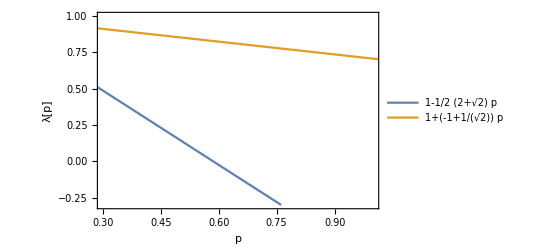

```mathematica
Plot[{1-1/2 (2+√2) p,1+(-1+1/(√2)) p},{p,-6.828427124746192,4-Sqrt[2]},Frame->True,FrameLabel->{"p","λ[p]"},
FrameStyle->Directive[Black,16],PlotLegends->"Expressions",
GridLines->{{2-Sqrt[2]},{}},
GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{.3,1},{-.3,1}}]
```

```mathematica
El valor máximo que puede tomar p para que la matriz sea positiva es 2-Sqrt[2]
Para ese valor
```

```mathematica
p=2-Sqrt[2];
```

```mathematica
M3dagM3 //FullSimplify
```

{{1/(√2),1-1/(√2)},{1-1/(√2),-2+3/(√2)}}

```mathematica
(* Utilizar esta medida para distinguir estados|0> y|+>,y comparar su eficiencia con una medida proyectiva estándar de un qubit.*)
```

```mathematica
El estado viene con igual probabilidad en 0 y en +
```

```mathematica
rho0p=(KroneckerProduct[st0,st0]/2)+(KroneckerProduct[stp,stp]/2)
```

{{3/4,1/4},{1/4,1/4}}

```mathematica
si medimos los proyectores P0 y P1
```

```mathematica
(* Se distingue que viene el estado |0> con probabilidad 1/4 cuando medis P1 porque al medir P0 no podés distinguir si vino |0> o|+>*)
```

```mathematica
Tr[rho0p]
```

1

```mathematica
Tr[P0.rho0p]
```

3/4

```mathematica
Tr[P1.rho0p]
```

1/4

```mathematica
P0+P1
```

{{1,0},{0,1}}

```mathematica
(* Paso lo mismo si se mide con los Pm y Pp. Se distingue que viene el estado |0> con probabilidad 1/4 cuando medis Pm porque al medir Pp no podés distinguir si vino |0> o|+>*)
```

```mathematica
Tr[Pm.rho0p]
```

1/4

```mathematica
Tr[Pp.rho0p]
```

3/4

```mathematica
Pp+Pm
```

{{1,0},{0,1}}

```mathematica
Clear[p]
Tr[M1dagM1.rho0p]
```

p/4

```mathematica
Tr[M2dagM2.rho0p]
```

p/4

```mathematica
Tr[M3dagM3.rho0p]//FullSimplify
```

1-p/2

## 4)Mostrar que sta=stppmm; pero rho01≠rhopm

```mathematica
sta=(st00+st11)/Sqrt[2]
```

{1/(√2),0,0,1/(√2)}

```mathematica
stp=(st0+st1)/Sqrt[2];stm=(st0-st1)/Sqrt[2]
```

{1/(√2),-1/(√2)}

```mathematica
stpp=KroneckerProduct[stp,stp];stmm=KroneckerProduct[stm,stm]
```

{{1/2,-1/2},{-1/2,1/2}}

```mathematica
stppmm=(stpp+stmm)/Sqrt[2]
```

{{1/(√2),0},{0,1/(√2)}}

```mathematica
rho01=(KroneckerProduct[st00,st00]+KroneckerProduct[st11,st11])/2
```

{{1/2,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1/2}}

```mathematica
rhopm=(KroneckerProduct[stpp,stpp]+KroneckerProduct[stmm,stmm])/2
```

{{1/4,0,0,1/4},{0,1/4,1/4,0},{0,1/4,1/4,0},{1/4,0,0,1/4}}

```mathematica
sx.st0
```

{0,1}

```mathematica
sy.st0
```

{0,ⅈ}

```mathematica
sp.st1
```

{1,0}

```mathematica
((sx+I sy)/2).stp
```

{1/(√2),0}

```mathematica
sm.stm
```

{0,1/(√2)}

```mathematica
stp
```

{1/(√2),1/(√2)}

```mathematica
sp.stp
```

{1/(√2),0}

```mathematica
sy
```

{{0,-ⅈ},{ⅈ,0}}

```mathematica
sm.stm
```

{0,1/(√2)}

```mathematica
Tr[rho01.KroneckerProduct[sp,sm]]
```

0

```mathematica
Tr[rhopm.KroneckerProduct[sp,sm]]
```

1/4

# II. Compuertas Cuánticas

## 1) Utilizando la notación X = σ x , Y = σ Y , Z = σ z , escribir las matrices que representan, en la base computacional {|00>, |01>, |10>, |11>), los operadores.

```mathematica
1)a)X ⊗ I
```

```mathematica
XI=MatrixForm[s1[1,4]]
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

```mathematica
b)I ⊗ X
```

```mathematica
IX=s1[4,1]
```

{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}}
```

```mathematica
IXinv=Transpose[IX]
```

{{0,1,0,0},{1,0,0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
IX.IXinv
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
c)X ⊗ X
```

```mathematica
XX=s1[1,1]
```

{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}

```mathematica
MatrixForm[XX]
```

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

```mathematica
XXinv=Transpose[XX]
```

{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}

```mathematica
XX.XXinv
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
c)Ux=P0⊗ I+P1⊗ X
```

```mathematica
P0={{1,0},{0,0}}
```

{{1,0},{0,0}}

```mathematica
MatrixForm[P0]
```

(1 | 0
0 | 0)

```mathematica
P1={{0,0},{0,1}}
```

{{0,0},{0,1}}

```mathematica
MatrixForm[P1]
```

(0 | 0
0 | 1)

```mathematica
Ux=KroneckerProduct[P0,s1[4]]+KroneckerProduct[P1,s1[1]]
```

{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}

```mathematica
MatrixForm[Ux]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
Ux.Transpose[Ux]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
(*Se trata del Control Not porque al 00 y 01 lo deja igual pero al 10 y 11 cambia el segundo*)
e1={1,0,0,0};e2={0,1,0,0};e3={0,0,1,0};e4={0,0,0,1};

Ux.e1
```

{1,0,0,0}

```mathematica
Ux.e2
```

{0,1,0,0}

```mathematica
Ux.e3
```

{0,0,0,1}

```mathematica
Ux.e4
```

{0,0,1,0}

```mathematica
e[1]=e1;e[2]=e2;e[3]=e3;e[4]=e4;
```

#### 2) Comprobar que W = U X (H ⊗ I), con H = (X + Z)/ 2 la compuerta de Hadamard, transforma la base computacional en la base de Bell, determinando su representación matricial. Concluir que una medición en la base de Bell (es decir, basada en proyectores ortogonales sobre estos estados) es equivalente a aplicar W † = (H ⊗ I)U X seguido de una medición en la base computacional (y una nueva aplicación de W ). Representar mediante un circuito la anterior equivalencia.

```mathematica
2) W=Ux(H⊗ I) transforma base computacional en base de Bell , con H=(X+Z)/Sqrt[2]
```

```mathematica
H=(s1[1]+s1[3])/Sqrt[2]
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

```mathematica
W=Ux.KroneckerProduct[H,s1[4]]
```

{{1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)},{0,1/(√2),0,-1/(√2)},{1/(√2),0,-1/(√2),0}}

```mathematica
MatrixForm[W]
```

```mathematica
W=({{1/(√2), 0, 1/(√2), 0}, {0, 1/(√2), 0, 1/(√2)}, {0, 1/(√2), 0, -1/(√2)}, {1/(√2), 0, -1/(√2), 0}})
```

{{1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)},{0,1/(√2),0,-1/(√2)},{1/(√2),0,-1/(√2),0}}

```mathematica
Bell[i_]=W.e[i]
```

{{1/(√2),0,1/(√2),0},{0,1/(√2),0,1/(√2)},{0,1/(√2),0,-1/(√2)},{1/(√2),0,-1/(√2),0}}.e[i]

```mathematica
Bell[1]
```

{1/(√2),0,0,1/(√2)}

```mathematica
Bell[2]
```

{0,1/(√2),1/(√2),0}

```mathematica
Bell[3]
```

{1/(√2),0,0,-1/(√2)}

```mathematica
Bell[4]
```

{0,1/(√2),-1/(√2),0}

```mathematica
Wtr=Transpose[W]
```

{{1/(√2),0,0,1/(√2)},{0,1/(√2),1/(√2),0},{1/(√2),0,0,-1/(√2)},{0,1/(√2),-1/(√2),0}}

```mathematica
Wtr.Bell[1]
```

{1,0,0,0}

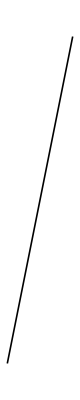

```mathematica
Gra=-Graphics-
```

### Mostrar que Us = UxŪxUx , con Ux = |0><0| ⊗ I + |1><1| ⊗ X y Ūx = I ⊗ |0><0| +X ⊗ |1><1|, es el operador de “swap”, que satisface Us|ab> = |ba> para todo estado producto |ab> = |a>|b>. Escribir la matriz que representa a Us en la base computacional y dibujar el circuito correspondiente.

```mathematica
3)Swap Us=Ux.Uxbar.Ux
```

```mathematica
Uxbar=KroneckerProduct[s1[4],P0]+KroneckerProduct[s1[1],P1]
```

{{1,0,0,0},{0,0,0,1},{0,0,1,0},{0,1,0,0}}

```mathematica
MatrixForm[Uxbar]
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

```mathematica
Us=Ux.Uxbar.Ux
```

{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}

```mathematica
Us.e1
```

{1,0,0,0}

```mathematica
Us.e2
```

{0,0,1,0}

```mathematica
Us.e3
```

{0,1,0,0}

```mathematica
Us.e4
```

{0,0,0,1}

```mathematica
Bonus: 
U x=(I⊗H)U z (I⊗H)  con U Z= |0><0|⊗I+ |1><1|⊗Z.
Interpretar y representar mediante un circuito.



IH=KroneckerProduct[s1[4],H]
{{1/(√2),1/(√2),0,0},{1/(√2),-1/(√2),0,0},{0,0,1/(√2),1/(√2)},{0,0,1/(√2),-1/(√2)}}

Uz=KroneckerProduct[P0,s1[4]]+KroneckerProduct[P1,s1[3]]

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}}

IH.Uz.IH
{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}


-Graphics-
```